## Тесты

#### Метод квадратур

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 1;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"quadrature.txt"]],Table[Real,n+1]];
```

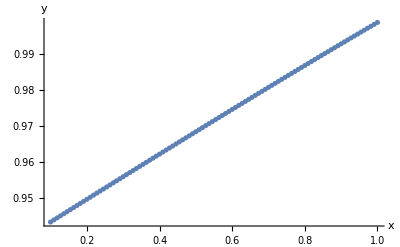

```mathematica
ListPlot[plots, AxesLabel->{"x","y"}, PlotRange->All]
```

#### Метод простой итерации

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 1;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"simple_iteration.txt"]],Table[Real,n+1]];
```

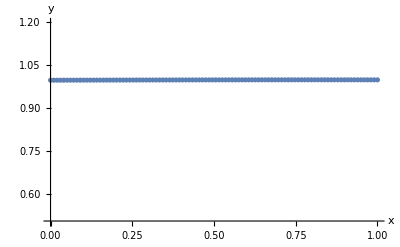

```mathematica
ListPlot[plots, AxesLabel->{"x","y"}, PlotRange->{0.5,1.2}]
```

#### Метод основанный на вырожденности ядра

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 1;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"degenerate_core.txt"]],Table[Real,n+1]];
```

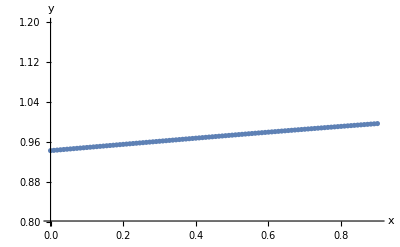

```mathematica
ListPlot[plots, AxesLabel->{"x","y"}, PlotRange->{0.8,1.2}]
```

```mathematica
Series[1/2(1-x Cos[s x]),{x,0,7},{s,0,7}]
```

1/2-x/2+(s^2/4+O[s]^8) x^3+(-s^4/48+O[s]^8) x^5+(s^6/1440+O[s]^8) x^7+O[x]^8

#### Решение

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"singular.txt"]],Table[Real,n+1]];
```

```mathematica
ListPointPlot3D[plots, PlotRange->All, ColorFunction->"Rainbow",AxesLabel->{"x1","x2"}]
```

-Graphics3D-

#### Ошибка

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Err.txt"]],Table[Real,n+1]];
```

```mathematica
ListPointPlot3D[plots, PlotRange->All, ColorFunction->"Rainbow",AxesLabel->{"x1","x2"}]
```

-Graphics3D-

## Проверка порядков

```mathematica
ClearAll["`*"];
```

```mathematica
NotebookDirectory[];
n = 1;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Error on diff step.txt"]],Table[Real,n+1]];
For[i=1,i≤5,i++,
Subscript[Err, i] = plots[[i]][[2]];]
```

```mathematica
GridData=Join[{{"τ, h_(1, 2)","AbsErr(τ, h_(1, 2))","Δ", "log_qΔ"}},Table[{{0.05 * (1/2)^(j-1),0.1*1/2^(j-1)},Subscript[Err, j],Subscript[Err, j]/Subscript[Err, j+1],Log[Subscript[Err, j]/Subscript[Err, j+1]]/Log[2]},{j,1,5}]];
```

```mathematica
Grid[GridData,Frame->All]
```

τ, h_(1, 2) | AbsErr(τ, h_(1, 2)) | Δ | log_qΔ
{0.05,0.1} | 0.0000640655 | 3.93378 | 1.97592
{0.025,0.05} | 0.000016286 | 3.9859 | 1.99491
{0.0125,0.025} | 4.0859×10^-6 | 3.99587 | 1.99851
{0.00625,0.0125} | 1.02253×10^-6 | 3.99905 | 1.99966
{0.003125,0.00625} | 2.55693×10^-7 | (2.55693×10^-7)/Err_6 | Log[(2.55693×10^-7)/Err_6]/Log[2]